# Combine Plots

```mathematica
ClearAll["Global`*"]
```

## Prerequisites

Need to run following codes to generate the data files:

High-T expansion result: phase_transition/highT.nb to generate phase_transition/output/highT.m
Instability scale solution: model_setup/instability.nb to generate model_setup/output/instable_scale.csv

## Instability scale

```mathematica
scalelist=Import[NotebookDirectory[]<>"/model_setup/output/instable_scale.csv"];
instable‵scale[mS_,sinθ_]:=Interpolation[scalelist][mS,sinθ];
```

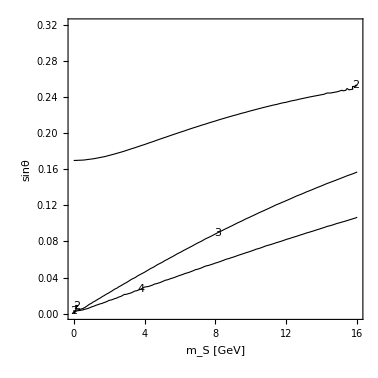

```mathematica
scale‵plot=ContourPlot[instable‵scale[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,Contours->{2,3,4},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

## High-T phase transition

```mathematica
DumpGet[NotebookDirectory[]<>"/phase_transition/output/highT.m"]
```

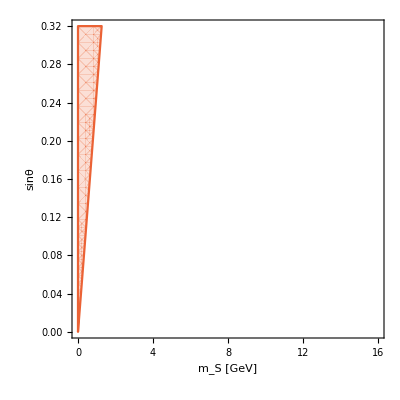

```mathematica
HighT‵SFOPT‵plot=RegionPlot[{strength[mS,sinθ]≤1.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[1]]];
non‵restore‵plot=RegionPlot[{Positive‵factor[mS,sinθ]≤0},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[4]],PlotStyle->{ColorData[97,"ColorList"][[4]],Opacity[0.2]}]
```

## LEP bound

```mathematica
boundlist=Import[NotebookDirectory[]<>"/collider/output/LEPbound.csv"];
boundfunc[mS_]:=Interpolation[boundlist][mS]
```

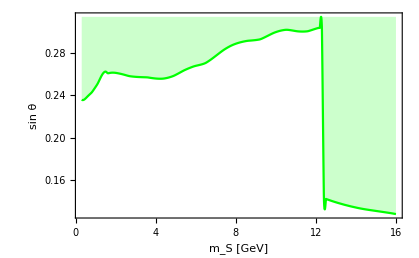

```mathematica
LEP‵plot=Plot[boundfunc[mS],{mS,0.3,16},Filling->Top,PlotStyle->Green,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

## LHC result

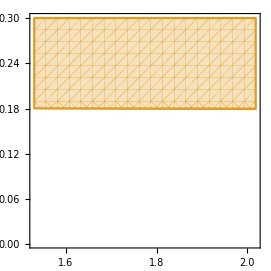

```mathematica
σggF=48.6;(*pb*)
σppH=55.1;(*pb*)
ΓSM=4.07*10^-3;(*GeV*)
mb=4.19;
mc=1.27;
mτ=1.78;
mμ=0.105;
ms=0.093;
mh=125.;
v=174.;
μBR[mS_]:=(mμ^2 Re[(mS^2-4 mμ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]+mμ^2 Re[(mS^2-4 mμ^2)^(3/2)]+3 ms^2 Re[(mS^2-4 ms^2)^(3/2)]);
τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
ghSS[mS_,sinθ_]:=2 √2 λ[mS,sinθ]v sinθ^2-√A2[mS,sinθ] sinθ;
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mh)√(1-4 mS^2/mh^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
dataset=Import[NotebookDirectory[]<>"collider/LHC.csv"];
limit[mS_]:=Interpolation[dataset][mS];
LHCplot=RegionPlot[σggF*BRhSS[mS,sinθ]*μBR[mS]^2>=10^-3 limit[mS],{mS,dataset[[1,1]],dataset[[-1,1]]},{sinθ,0.001,0.3},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["",FontFamily->"Times",FontSize->18],Style["",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,"ColorList"][[2]],Opacity[0.3]},BoundaryStyle->{ColorData[97,"ColorList"][[2]]}]
```

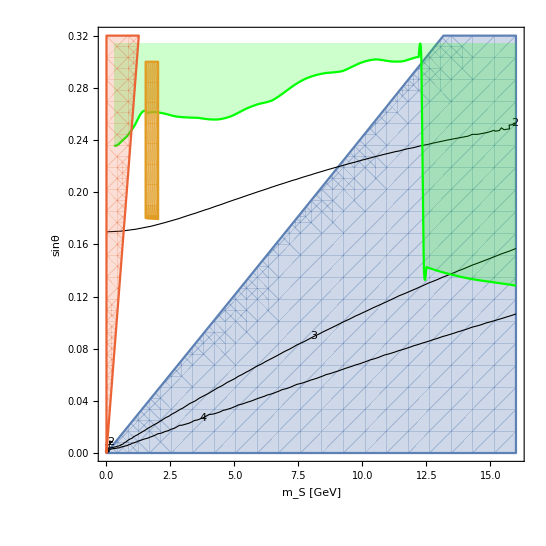

```mathematica
Show[HighT‵SFOPT‵plot,scale‵plot,LEP‵plot,LHCplot,non‵restore‵plot]
```